```mathematica
(*matrix transformations, rotation, translation, scaling*)
```

-Graphics-

```mathematica
Clear["Global`*"];
```

```mathematica
M={{xx,yx,zx,ox},{xy,yy,zy,oy},{xz,yz,zz,oz},{xo,yo,zo,oo}};M//MatrixForm
```

(xx | yx | zx | ox
xy | yy | zy | oy
xz | yz | zz | oz
xo | yo | zo | oo)

```mathematica
{a,b,c,1}.M//Column
```

xo+a xx+b xy+c xz
yo+a yx+b yy+c yz
zo+a zx+b zy+c zz
oo+a ox+b oy+c oz

```mathematica
M.{a,b,c,1}//Column
```

ox+a xx+b yx+c zx
oy+a xy+b yy+c zy
oz+a xz+b yz+c zz
oo+a xo+b yo+c zo

```mathematica
s;(*scale*)
S={{sx,0,0,0},{0,sy,0,0},{0,0,sz,0},{0,0,0,1}};
S//MatrixForm
S.{a,b,c,1}//Column
```

(sx | 0 | 0 | 0
0 | sy | 0 | 0
0 | 0 | sz | 0
0 | 0 | 0 | 1)

a sx
b sy
c sz
1

```mathematica
γ;(*rotation of z-axis*)
Rγ=PadRight[RotationMatrix[γ,{0,0,1}],{4,4}];
Rγ[[4,4]]=1;
Rγ//MatrixForm
Rγ.S.{a,b,c,1}//Column
```

(Cos[γ] | -Sin[γ] | 0 | 0
Sin[γ] | Cos[γ] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

a sx Cos[γ]-b sy Sin[γ]
b sy Cos[γ]+a sx Sin[γ]
c sz
1

```mathematica
α;(*rotation of x-axis*)
Rα=PadRight[RotationMatrix[α,{1,0,0}],{4,4}];
Rα[[4,4]]=1;
Rα//MatrixForm
Rα.Rγ.S.{a,b,c,1}//Column
```

(1 | 0 | 0 | 0
0 | Cos[α] | -Sin[α] | 0
0 | Sin[α] | Cos[α] | 0
0 | 0 | 0 | 1)

a sx Cos[γ]-b sy Sin[γ]
b sy Cos[α] Cos[γ]-c sz Sin[α]+a sx Cos[α] Sin[γ]
c sz Cos[α]+b sy Cos[γ] Sin[α]+a sx Sin[α] Sin[γ]
1

```mathematica
β;(*rotation of y-axis*)
Rβ=PadRight[RotationMatrix[β,{0,1,0}],{4,4}];
Rβ[[4,4]]=1;
Rβ//MatrixForm
Rβ.Rα.Rγ.S.{a,b,c,1}//Column
```

(Cos[β] | 0 | Sin[β] | 0
0 | 1 | 0 | 0
-Sin[β] | 0 | Cos[β] | 0
0 | 0 | 0 | 1)

c sz Cos[α] Sin[β]+b sy (Cos[γ] Sin[α] Sin[β]-Cos[β] Sin[γ])+a sx (Cos[β] Cos[γ]+Sin[α] Sin[β] Sin[γ])
b sy Cos[α] Cos[γ]-c sz Sin[α]+a sx Cos[α] Sin[γ]
c sz Cos[α] Cos[β]+a sx (-Cos[γ] Sin[β]+Cos[β] Sin[α] Sin[γ])+b sy (Cos[β] Cos[γ] Sin[α]+Sin[β] Sin[γ])
1

```mathematica
TranslationTransform[{tx,ty,tz}]
```

TransformationFunction[(1 | 0 | 0 | tx
0 | 1 | 0 | ty
0 | 0 | 1 | tz
0 | 0 | 0 | 1)]

```mathematica
t;(*translation*)
T ={{1,0,0,tx},{0,1,0,ty},{0,0,1,tz},{0,0,0,1}};
T//MatrixForm
T.Rβ.Rα.Rγ.S.{a,b,c,1}//Column
```

(1 | 0 | 0 | tx
0 | 1 | 0 | ty
0 | 0 | 1 | tz
0 | 0 | 0 | 1)

tx+c sz Cos[α] Sin[β]+b sy (Cos[γ] Sin[α] Sin[β]-Cos[β] Sin[γ])+a sx (Cos[β] Cos[γ]+Sin[α] Sin[β] Sin[γ])
ty+b sy Cos[α] Cos[γ]-c sz Sin[α]+a sx Cos[α] Sin[γ]
tz+c sz Cos[α] Cos[β]+a sx (-Cos[γ] Sin[β]+Cos[β] Sin[α] Sin[γ])+b sy (Cos[β] Cos[γ] Sin[α]+Sin[β] Sin[γ])
1

```mathematica
T.Rβ.Rα.Rγ.S.{a,b,c,1}==T.Rβ.Rα.Rγ.(S.{a,b,c,1})
T.Rβ.Rα.Rγ.S.{a,b,c,1}==(T.Rβ.Rα.Rγ.S).{a,b,c,1}
T.Rβ.Rα.Rγ.S.{a,b,c,1}==(T.Rβ.Rα.Rγ).S.{a,b,c,1}
T.Rβ.Rα.Rγ.S.{a,b,c,1}==(T.Rβ.Rα).Rγ.S.{a,b,c,1}
T.Rβ.Rα.Rγ.S.{a,b,c,1}==((((T.Rβ).Rα).Rγ).S).{a,b,c,1}
T.Rβ.Rα.Rγ.S.{a,b,c,1}==T.Rβ.Rα.Rγ.(S.{a,b,c,1})
T.Rβ.Rα.Rγ.S.{a,b,c,1}==(((T.Rβ).Rα).Rγ).(S.{a,b,c,1})
```

True

True

True

«4 more identical outputs»

```mathematica
A=RotationMatrix[γ,{0,0,1}][[1;;2,1;;2]]
A.Transpose[A]==Transpose[A].A
A.Transpose[A]==IdentityMatrix[2]
```

{{Cos[γ],-Sin[γ]},{Sin[γ],Cos[γ]}}

True

{{Cos[γ]^2+Sin[γ]^2,0},{0,Cos[γ]^2+Sin[γ]^2}}=={{1,0},{0,1}}

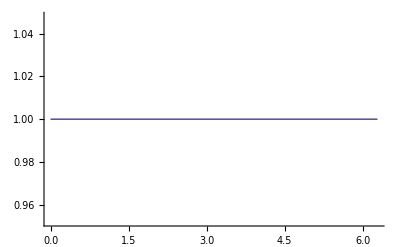

```mathematica
Plot[Cos[γ]^2+Sin[γ]^2,{γ,0,2π}]
```

```mathematica
R={{Cos[γ],-Sin[γ]},{Sin[γ],Cos[γ]}}
```

{{Cos[γ],-Sin[γ]},{Sin[γ],Cos[γ]}}

```mathematica
R^-1
```

{{Sec[γ],-Csc[γ]},{Csc[γ],Sec[γ]}}

```mathematica
(R^-1).R
```

{{0,-Cot[γ]-Tan[γ]},{Cot[γ]+Tan[γ],0}}

```mathematica
Rγ
Transpose[Rγ]
Inverse[Rγ]
Transpose[Rγ].Rγ
```

{{Cos[γ],-Sin[γ],0,0},{Sin[γ],Cos[γ],0,0},{0,0,1,0},{0,0,0,1}}

{{Cos[γ],Sin[γ],0,0},{-Sin[γ],Cos[γ],0,0},{0,0,1,0},{0,0,0,1}}

{{Cos[γ]/(Cos[γ]^2+Sin[γ]^2),Sin[γ]/(Cos[γ]^2+Sin[γ]^2),0,0},{-Sin[γ]/(Cos[γ]^2+Sin[γ]^2),Cos[γ]/(Cos[γ]^2+Sin[γ]^2),0,0},{0,0,1,0},{0,0,0,1}}

{{Cos[γ]^2+Sin[γ]^2,0,0,0},{0,Cos[γ]^2+Sin[γ]^2,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(*Transpose[T.Rβ.Rα.Rγ.S]==Inverse[T.Rβ.Rα.Rγ.S]*)
```

```mathematica
M.S//MatrixForm
```

(sx xx | sy yx | sz zx | ox
sx xy | sy yy | sz zy | oy
sx xz | sy yz | sz zz | oz
sx xo | sy yo | sz zo | oo)

```mathematica
M.Rγ//MatrixForm
```

(xx Cos[γ]+yx Sin[γ] | yx Cos[γ]-xx Sin[γ] | zx | ox
xy Cos[γ]+yy Sin[γ] | yy Cos[γ]-xy Sin[γ] | zy | oy
xz Cos[γ]+yz Sin[γ] | yz Cos[γ]-xz Sin[γ] | zz | oz
xo Cos[γ]+yo Sin[γ] | yo Cos[γ]-xo Sin[γ] | zo | oo)

```mathematica
M.Rα//MatrixForm
```

(xx | yx Cos[α]+zx Sin[α] | zx Cos[α]-yx Sin[α] | ox
xy | yy Cos[α]+zy Sin[α] | zy Cos[α]-yy Sin[α] | oy
xz | yz Cos[α]+zz Sin[α] | zz Cos[α]-yz Sin[α] | oz
xo | yo Cos[α]+zo Sin[α] | zo Cos[α]-yo Sin[α] | oo)

```mathematica
M.Rβ//MatrixForm
```

(xx Cos[β]-zx Sin[β] | yx | zx Cos[β]+xx Sin[β] | ox
xy Cos[β]-zy Sin[β] | yy | zy Cos[β]+xy Sin[β] | oy
xz Cos[β]-zz Sin[β] | yz | zz Cos[β]+xz Sin[β] | oz
xo Cos[β]-zo Sin[β] | yo | zo Cos[β]+xo Sin[β] | oo)

```mathematica
M.T//MatrixForm
```

(xx | yx | zx | ox+tx xx+ty yx+tz zx
xy | yy | zy | oy+tx xy+ty yy+tz zy
xz | yz | zz | oz+tx xz+ty yz+tz zz
xo | yo | zo | oo+tx xo+ty yo+tz zo)

```mathematica
Mmw=T.Rβ.Rα.Rγ.S;
Mmw//MatrixForm
```

(sx (Cos[β] Cos[γ]+Sin[α] Sin[β] Sin[γ]) | sy (Cos[γ] Sin[α] Sin[β]-Cos[β] Sin[γ]) | sz Cos[α] Sin[β] | tx
sx Cos[α] Sin[γ] | sy Cos[α] Cos[γ] | -sz Sin[α] | ty
sx (-Cos[γ] Sin[β]+Cos[β] Sin[α] Sin[γ]) | sy (Cos[β] Cos[γ] Sin[α]+Sin[β] Sin[γ]) | sz Cos[α] Cos[β] | tz
0 | 0 | 0 | 1)

```mathematica
S.Rγ.Rα.Rβ.T//MatrixForm
```

(sx Cos[β] Cos[γ]-sx Sin[α] Sin[β] Sin[γ] | -sx Cos[α] Sin[γ] | sx Cos[γ] Sin[β]+sx Cos[β] Sin[α] Sin[γ] | -sx ty Cos[α] Sin[γ]+tz (sx Cos[γ] Sin[β]+sx Cos[β] Sin[α] Sin[γ])+tx (sx Cos[β] Cos[γ]-sx Sin[α] Sin[β] Sin[γ])
sy Cos[γ] Sin[α] Sin[β]+sy Cos[β] Sin[γ] | sy Cos[α] Cos[γ] | -sy Cos[β] Cos[γ] Sin[α]+sy Sin[β] Sin[γ] | sy ty Cos[α] Cos[γ]+tx (sy Cos[γ] Sin[α] Sin[β]+sy Cos[β] Sin[γ])+tz (-sy Cos[β] Cos[γ] Sin[α]+sy Sin[β] Sin[γ])
-sz Cos[α] Sin[β] | sz Sin[α] | sz Cos[α] Cos[β] | sz tz Cos[α] Cos[β]+sz ty Sin[α]-sz tx Cos[α] Sin[β]
0 | 0 | 0 | 1)

```mathematica
(*orthogonal matrix*)
Q=IdentityMatrix[4];
Q//MatrixForm
Transpose[Q]==Inverse[Q]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

True

```mathematica
Q=Rγ
Transpose[Q]==Inverse[Q]
Q//MatrixForm
```

{{Cos[γ],-Sin[γ],0,0},{Sin[γ],Cos[γ],0,0},{0,0,1,0},{0,0,0,1}}

{{Cos[γ],Sin[γ],0,0},{-Sin[γ],Cos[γ],0,0},{0,0,1,0},{0,0,0,1}}=={{Cos[γ]/(Cos[γ]^2+Sin[γ]^2),Sin[γ]/(Cos[γ]^2+Sin[γ]^2),0,0},{-Sin[γ]/(Cos[γ]^2+Sin[γ]^2),Cos[γ]/(Cos[γ]^2+Sin[γ]^2),0,0},{0,0,1,0},{0,0,0,1}}

(Cos[γ] | -Sin[γ] | 0 | 0
Sin[γ] | Cos[γ] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Q=Mmw;
Transpose[Q]==Inverse[Q]
```

{{sx (Cos[β] Cos[γ]+Sin[α] Sin[β] Sin[γ]),sx Cos[α] Sin[γ],sx (-Cos[γ] Sin[β]+Cos[β] Sin[α] Sin[γ]),0},{sy (Cos[γ] Sin[α] Sin[β]-Cos[β] Sin[γ]),sy Cos[α] Cos[γ],sy (Cos[β] Cos[γ] Sin[α]+Sin[β] Sin[γ]),0},{sz Cos[α] Sin[β],-sz Sin[α],sz Cos[α] Cos[β],0},{tx,ty,tz,1}}=={{(sy sz Cos[α]^2 Cos[β] Cos[γ]+sy sz Cos[β] Cos[γ] Sin[α]^2+sy sz Sin[α] Sin[β] Sin[γ])/(sx sy sz Cos[α]^2 Cos[β]^2 Cos[γ]^2+sx sy sz Cos[β]^2 Cos[γ]^2 Sin[α]^2+sx sy sz Cos[α]^2 Cos[γ]^2 Sin[β]^2+sx sy sz Cos[γ]^2 Sin[α]^2 Sin[β]^2+sx sy sz Cos[α]^2 Cos[β]^2 Sin[γ]^2+sx sy sz Cos[β]^2 Sin[α]^2 Sin[γ]^2+sx sy sz Cos[α]^2 Sin[β]^2 Sin[γ]^2+sx sy sz Sin[α]^2 Sin[β]^2 Sin[γ]^2),(sy sz Cos[α] Cos[β]^2 Sin[γ]+sy sz Cos[α] Sin[β]^2 Sin[γ])/(sx sy sz Cos[α]^2 Cos[β]^2 Cos[γ]^2+sx sy sz Cos[β]^2 Cos[γ]^2 Sin[α]^2+sx sy sz Cos[α]^2 Cos[γ]^2 Sin[β]^2+sx sy sz Cos[γ]^2 Sin[α]^2 Sin[β]^2+sx sy sz Cos[α]^2 Cos[β]^2 Sin[γ]^2+sx sy sz Cos[β]^2 Sin[α]^2 Sin[γ]^2+sx sy sz Cos[α]^2 Sin[β]^2 Sin[γ]^2+sx sy sz Sin[α]^2 Sin[β]^2 Sin[γ]^2),(-sy sz Cos[α]^2 Cos[γ] Sin[β]-sy sz Cos[γ] Sin[α]^2 Sin[β]+sy sz Cos[β] Sin[α] Sin[γ])/(sx sy sz Cos[α]^2 Cos[β]^2 Cos[γ]^2+sx sy sz Cos[β]^2 Cos[γ]^2 Sin[α]^2+sx sy sz Cos[α]^2 Cos[γ]^2 Sin[β]^2+sx sy sz Cos[γ]^2 Sin[α]^2 Sin[β]^2+sx sy sz Cos[α]^2 Cos[β]^2 Sin[γ]^2+sx sy sz Cos[β]^2 Sin[α]^2 Sin[γ]^2+sx sy sz Cos[α]^2 Sin[β]^2 Sin[γ]^2+sx sy sz Sin[α]^2 Sin[β]^2 Sin[γ]^2),(-sy sz tx Cos[α]^2 Cos[β] Cos[γ]-sy sz tx Cos[β] Cos[γ] Sin[α]^2+sy sz tz Cos[α]^2 Cos[γ] Sin[β]+sy sz tz Cos[γ] Sin[α]^2 Sin[β]-sy sz ty Cos[α] Cos[β]^2 Sin[γ]-sy sz tz Cos[β] Sin[α] Sin[γ]-sy sz tx Sin[α] Sin[β] Sin[γ]-sy sz ty Cos[α] Sin[β]^2 Sin[γ])/(sx sy sz Cos[α]^2 Cos[β]^2 Cos[γ]^2+sx sy sz Cos[β]^2 Cos[γ]^2 Sin[α]^2+sx sy sz Cos[α]^2 Cos[γ]^2 Sin[β]^2+sx sy sz Cos[γ]^2 Sin[α]^2 Sin[β]^2+sx sy sz Cos[α]^2 Cos[β]^2 Sin[γ]^2+sx sy sz Cos[β]^2 Sin[α]^2 Sin[γ]^2+sx sy sz Cos[α]^2 Sin[β]^2 Sin[γ]^2+sx sy sz Sin[α]^2 Sin[β]^2 Sin[γ]^2)},{(sx sz Cos[γ] Sin[α] Sin[β]-sx sz Cos[α]^2 Cos[β] Sin[γ]-sx sz Cos[β] Sin[α]^2 Sin[γ])/(sx sy sz Cos[α]^2 Cos[β]^2 Cos[γ]^2+sx sy sz Cos[β]^2 Cos[γ]^2 Sin[α]^2+sx sy sz Cos[α]^2 Cos[γ]^2 Sin[β]^2+sx sy sz Cos[γ]^2 Sin[α]^2 Sin[β]^2+sx sy sz Cos[α]^2 Cos[β]^2 Sin[γ]^2+sx sy sz Cos[β]^2 Sin[α]^2 Sin[γ]^2+sx sy sz Cos[α]^2 Sin[β]^2 Sin[γ]^2+sx sy sz Sin[α]^2 Sin[β]^2 Sin[γ]^2),(sx sz Cos[α] Cos[β]^2 Cos[γ]+sx sz Cos[α] Cos[γ] Sin[β]^2)/(sx sy sz Cos[α]^2 Cos[β]^2 Cos[γ]^2+sx sy sz Cos[β]^2 Cos[γ]^2 Sin[α]^2+sx sy sz Cos[α]^2 Cos[γ]^2 Sin[β]^2+sx sy sz Cos[γ]^2 Sin[α]^2 Sin[β]^2+sx sy sz Cos[α]^2 Cos[β]^2 Sin[γ]^2+sx sy sz Cos[β]^2 Sin[α]^2 Sin[γ]^2+sx sy sz Cos[α]^2 Sin[β]^2 Sin[γ]^2+sx sy sz Sin[α]^2 Sin[β]^2 Sin[γ]^2),(sx sz Cos[β] Cos[γ] Sin[α]+sx sz Cos[α]^2 Sin[β] Sin[γ]+sx sz Sin[α]^2 Sin[β] Sin[γ])/(sx sy sz Cos[α]^2 Cos[β]^2 Cos[γ]^2+sx sy sz Cos[β]^2 Cos[γ]^2 Sin[α]^2+sx sy sz Cos[α]^2 Cos[γ]^2 Sin[β]^2+sx sy sz Cos[γ]^2 Sin[α]^2 Sin[β]^2+sx sy sz Cos[α]^2 Cos[β]^2 Sin[γ]^2+sx sy sz Cos[β]^2 Sin[α]^2 Sin[γ]^2+sx sy sz Cos[α]^2 Sin[β]^2 Sin[γ]^2+sx sy sz Sin[α]^2 Sin[β]^2 Sin[γ]^2),(-sx sz ty Cos[α] Cos[β]^2 Cos[γ]-sx sz tz Cos[β] Cos[γ] Sin[α]-sx sz tx Cos[γ] Sin[α] Sin[β]-sx sz ty Cos[α] Cos[γ] Sin[β]^2+sx sz tx Cos[α]^2 Cos[β] Sin[γ]+sx sz tx Cos[β] Sin[α]^2 Sin[γ]-sx sz tz Cos[α]^2 Sin[β] Sin[γ]-sx sz tz Sin[α]^2 Sin[β] Sin[γ])/(sx sy sz Cos[α]^2 Cos[β]^2 Cos[γ]^2+sx sy sz Cos[β]^2 Cos[γ]^2 Sin[α]^2+sx sy sz Cos[α]^2 Cos[γ]^2 Sin[β]^2+sx sy sz Cos[γ]^2 Sin[α]^2 Sin[β]^2+sx sy sz Cos[α]^2 Cos[β]^2 Sin[γ]^2+sx sy sz Cos[β]^2 Sin[α]^2 Sin[γ]^2+sx sy sz Cos[α]^2 Sin[β]^2 Sin[γ]^2+sx sy sz Sin[α]^2 Sin[β]^2 Sin[γ]^2)},{(sx sy Cos[α] Cos[γ]^2 Sin[β]+sx sy Cos[α] Sin[β] Sin[γ]^2)/(sx sy sz Cos[α]^2 Cos[β]^2 Cos[γ]^2+sx sy sz Cos[β]^2 Cos[γ]^2 Sin[α]^2+sx sy sz Cos[α]^2 Cos[γ]^2 Sin[β]^2+sx sy sz Cos[γ]^2 Sin[α]^2 Sin[β]^2+sx sy sz Cos[α]^2 Cos[β]^2 Sin[γ]^2+sx sy sz Cos[β]^2 Sin[α]^2 Sin[γ]^2+sx sy sz Cos[α]^2 Sin[β]^2 Sin[γ]^2+sx sy sz Sin[α]^2 Sin[β]^2 Sin[γ]^2),(-sx sy Cos[β]^2 Cos[γ]^2 Sin[α]-sx sy Cos[γ]^2 Sin[α] Sin[β]^2-sx sy Cos[β]^2 Sin[α] Sin[γ]^2-sx sy Sin[α] Sin[β]^2 Sin[γ]^2)/(sx sy sz Cos[α]^2 Cos[β]^2 Cos[γ]^2+sx sy sz Cos[β]^2 Cos[γ]^2 Sin[α]^2+sx sy sz Cos[α]^2 Cos[γ]^2 Sin[β]^2+sx sy sz Cos[γ]^2 Sin[α]^2 Sin[β]^2+sx sy sz Cos[α]^2 Cos[β]^2 Sin[γ]^2+sx sy sz Cos[β]^2 Sin[α]^2 Sin[γ]^2+sx sy sz Cos[α]^2 Sin[β]^2 Sin[γ]^2+sx sy sz Sin[α]^2 Sin[β]^2 Sin[γ]^2),(sx sy Cos[α] Cos[β] Cos[γ]^2+sx sy Cos[α] Cos[β] Sin[γ]^2)/(sx sy sz Cos[α]^2 Cos[β]^2 Cos[γ]^2+sx sy sz Cos[β]^2 Cos[γ]^2 Sin[α]^2+sx sy sz Cos[α]^2 Cos[γ]^2 Sin[β]^2+sx sy sz Cos[γ]^2 Sin[α]^2 Sin[β]^2+sx sy sz Cos[α]^2 Cos[β]^2 Sin[γ]^2+sx sy sz Cos[β]^2 Sin[α]^2 Sin[γ]^2+sx sy sz Cos[α]^2 Sin[β]^2 Sin[γ]^2+sx sy sz Sin[α]^2 Sin[β]^2 Sin[γ]^2),(-sx sy tz Cos[α] Cos[β] Cos[γ]^2+sx sy ty Cos[β]^2 Cos[γ]^2 Sin[α]-sx sy tx Cos[α] Cos[γ]^2 Sin[β]+sx sy ty Cos[γ]^2 Sin[α] Sin[β]^2-sx sy tz Cos[α] Cos[β] Sin[γ]^2+sx sy ty Cos[β]^2 Sin[α] Sin[γ]^2-sx sy tx Cos[α] Sin[β] Sin[γ]^2+sx sy ty Sin[α] Sin[β]^2 Sin[γ]^2)/(sx sy sz Cos[α]^2 Cos[β]^2 Cos[γ]^2+sx sy sz Cos[β]^2 Cos[γ]^2 Sin[α]^2+sx sy sz Cos[α]^2 Cos[γ]^2 Sin[β]^2+sx sy sz Cos[γ]^2 Sin[α]^2 Sin[β]^2+sx sy sz Cos[α]^2 Cos[β]^2 Sin[γ]^2+sx sy sz Cos[β]^2 Sin[α]^2 Sin[γ]^2+sx sy sz Cos[α]^2 Sin[β]^2 Sin[γ]^2+sx sy sz Sin[α]^2 Sin[β]^2 Sin[γ]^2)},{0,0,0,1}}